```mathematica
Manipulate[∑_(i=1)^n i^(1/2),{n,1,k,1},{k,1,50}]
```

```mathematica
Manipulate[∑_(t=1)^n Gamma[t+1]/Gamma[t+1/2],{n,1,k,1},{k,1,50}]
```

```mathematica
N[Manipulate[∑_(i=1)^n i^(1/2),{n,1,k,1},{k,1,50}]]
```

NSum::nslim: Limit of summation n is not a number.

```mathematica
N[Manipulate[∑_(t=1)^n Gamma[t+1]/Gamma[t+1/2],{n,1,k,1},{k,1,50}]]
```

NSum::nslim: Limit of summation n is not a number.

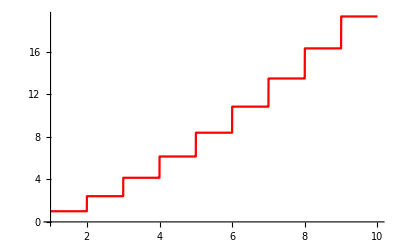

```mathematica
p1=Plot[∑_(i=1)^n i^(1/2),{n,1,10},PlotStyle->Red]
```

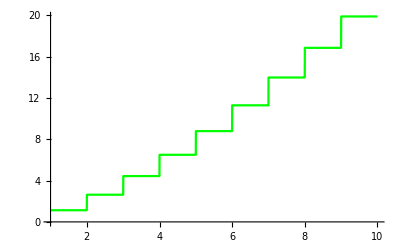

```mathematica
p2=Plot[∑_(t=1)^n Gamma[t+1]/Gamma[t+1/2],{n,1,10},PlotStyle->Green]
```

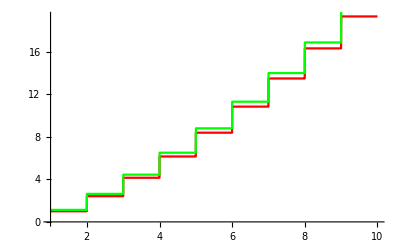

```mathematica
Show[p1,p2]
```

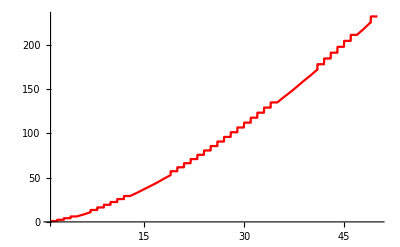

```mathematica
p3=Plot[∑_(i=1)^n i^(1/2),{n,1,50},PlotStyle->Red]
```

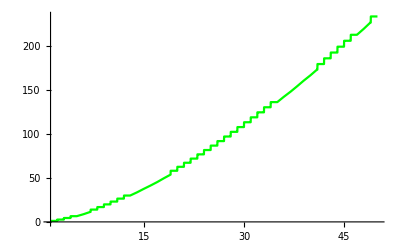

```mathematica
p4=Plot[∑_(t=1)^n Gamma[t+1]/Gamma[t+1/2],{n,1,50},PlotStyle->Green]
```

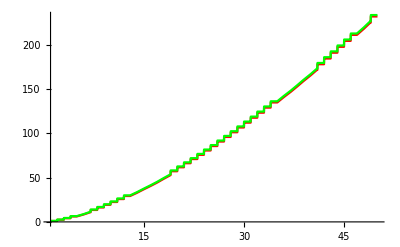

```mathematica
Show[p3,p4]
```